40/3 | 13
10 | 9
8 | 7
20/3 | 5
5 | 3

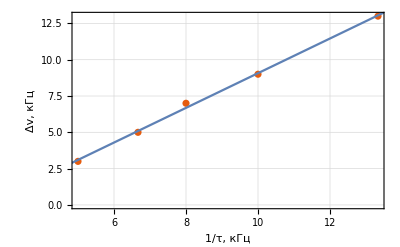

-2.87017+1.19421 x

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.87017 | 0.289474 | -9.91514 | 0.0021822
x | 1.19421 | 0.0319195 | 37.4131 | 0.0000420034

```mathematica
Table1 = {{75, 100, 125, 150, 200}, {13, 9, 7, 5, 3}, {□, □, □, □, □}};
For[i = 1, i≤5, i++, Table1[[3,i]]=1/Table1[[1,i]]*1000];
ApproximatedPart = Delete[Table1, {1}];
ApproximatedPart = Transpose[ApproximatedPart];
ClearAll[ApproximatedLine];
ApproximatedPart[[All, {1,2}]] = ApproximatedPart[[All, {2,1}]];
ApproximatedLine = LinearModelFit[ApproximatedPart,x,x];
ApproximatedPart//Grid
Show[ListPlot[ApproximatedPart, PlotTheme->"Scientific", GridLines->Automatic], Plot[ApproximatedLine[x], {x,3,14}], FrameLabel->{{HoldForm["Δv, кГц"],None},{RawBoxes[ RowBox[{"1","/","τ", ",", " ","кГц"}]], None}}]
Export["3.6.1 Graph 1.pdf", %];
ApproximatedLine["BestFit"]
Export["approx 1 tex.txt", TeXForm[ApproximatedLine["BestFit"]]];
ApproximatedLine["ParameterTable"]
Export["Approximation Parameters 1.pdf",ApproximatedLine["ParameterTable"]];
```

1 | 1
2 | 15/8
3 | 25/8
4 | 15/4
5 | 5
6 | 25/4
7 | 55/8
8 | 65/8

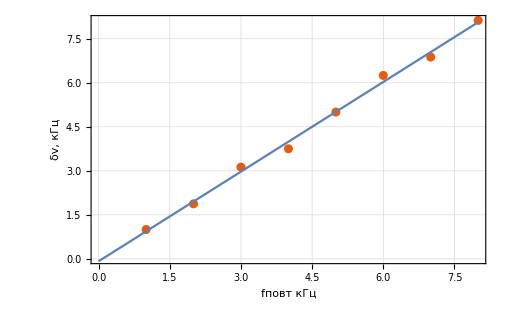

-0.0803571+1.01786 x

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0803571 | 0.132733 | -0.605406 | 0.567088
x | 1.01786 | 0.026285 | 38.7239 | 1.98097×10^-8

```mathematica
Table1 = {{1, 2, 3, 4, 5, 6, 7, 8}, {□, 3, 5, 6, 8, 10, 11, 13}, {1, □, □, □, □, □, □, □}};
For[i = 2, i≤8, i++, Table1[[3,i]]=Table1[[2,i]]/8*5];
ApproximatedPart = Delete[Table1, {2}];
ApproximatedPart = Transpose[ApproximatedPart];
ClearAll[ApproximatedLine];
ApproximatedLine = LinearModelFit[ApproximatedPart,x,x];
ApproximatedPart//Grid
Show[ListPlot[ApproximatedPart, PlotTheme->"Scientific", GridLines->Automatic], Plot[ApproximatedLine[x], {x,0,8}], FrameLabel->{{HoldForm["δv, кГц"],None},{RawBoxes[ RowBox[{ "f", "повт", " ","кГц"}]], None}}]
Export["3.6.1 Graph 2.pdf", %];
ApproximatedLine["BestFit"]
Export["approx 2 tex.txt", TeXForm[ApproximatedLine["BestFit"]]];
ApproximatedLine["ParameterTable"]
Export["Approximation Parameters 2.pdf",ApproximatedLine["ParameterTable"]];
```